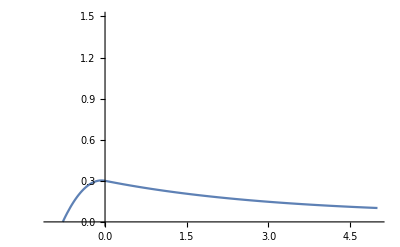

```mathematica
α1=0.1;
αlow=0.01;
m0=0.005;
M0=1.2;
α2=0.3;
ep=0.05;

f[x_]=Which[x<0,-M0/αlow +(α2+M0/αlow)Cos[Sqrt[αlow]x]-(α2-m0/α1)Sqrt[α1/αlow]Sin[Sqrt[αlow]x],True,m0/α1+(α2-m0/α1)Exp[-Sqrt[α1]x]];
Plot[f[x],{x,-1,5},PlotRange->{0,1.5}]
```

InterpolatingFunction[…]

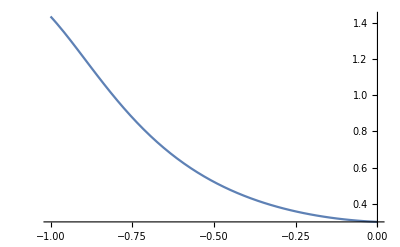

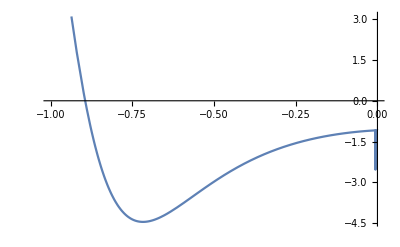

```mathematica
U1=NDSolveValue[{-ep u''[x]==-(u[x]-0.1)(1.2-u[x])(u[x]+αlow),u[0]==α2,u'[0]==-(α2-m0/α1)Sqrt[α1]},u,{x,-1,0}]
Plot[U1[x],{x,-1,0}]
Plot[-U1''[x]+α1 U1[x],{x,-1,0}]
```